# Physics 230 -- Lab 8 (Programming II)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics and Astronomy, Fall 2011

In this lab, we will look at strategies to deal with challenges which arise when Mathematica programs start getting more complex than the very simple ones we’ve mostly encountered so far.  The ideas we will introduce are scoping of names, encapsulating code in units, creating reusable code, and documenting code.  There are two major topics important in complex problems we won’t be able to consider until a later lab: debugging and testing.

The first challenge with complex problems is that symbols we’ve used with a particular meaning in one place have a different meaning in another.  These conflicting names can sometimes interfer with each other causing incorrect answers.  Limiting the scope of name definitions to the parts of the code where we need them is called scoping.

The second challenge we face is the needs to organize code we need to use into self-contained units.  We will learn how to do this using modules and contexts.

As you use Mathematica more and more in your physics work, you’ll find yourself accumlating functions and modules which you want to use again and again.  Perhaps you’ll write some very helpful to a group of people and would like to share it with them.  We’ll learn a good way to do this using packages with appropriate documentation.

## Scoping Constructs (45 min)

We often find it useful to define a "local" variable inside a specific function, so that we can safely use the same "global" variable name on the outside without conflicts.  Structures that allow us to thus restrict the "scope" of a variable are called "scoping constructs".  Another way to manage the scope of names is using Contexts.  We’ll start with scoping constructs.

### (#1) Local variables that you have already seen (5 min)

(a) You have already seen local variables as iterators in loop structures like Table, Sum, Plot and Do.  Evaluate the examples below, and observe that local variable n inside the loops does not interact with global variable n on the outside.  In this sense, these loop structures are also scoping constructs.

{1,4,9,16,25,36,49,64,81,100}

385

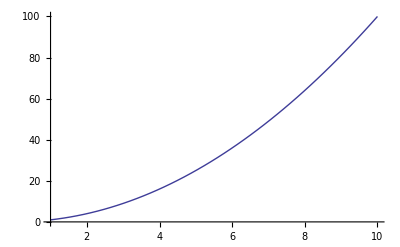

1

2

3

4

5

6

7

8

9

10

3

```mathematica
n = 3;

Table[n^2,{n,1,10}]
Sum[n^2,{n,1,10}]
Plot[n^2,{n,1,10}]
Do[Print[n],{n,1,10}]

n
```

(b) Because the For loop structure uses a global variable as its iterator, it is more susceptible to variable-name conflicts.  Can you see problem in the subsequent integral?

```mathematica
For[n=0, n<10, n++, "do nothing"]
Integrate[n^2,n]
```

Integrate::ilim: Invalid integration variable or limit(s) in TraditionalForm`10.

∫100ⅆ10

(c) We use local variables to train a function to take an argument.  When we use a pattern (i.e. "n_")  to define a function, n behaves as a strictly local variable inside that function.  In the example below, observe that the local variable n inside of f does not conflict with the global n on the outside.

```mathematica
n = 3
f[n_] := 5*n
f[n]
f[2]
```

3

15

10

(d) Clear a few variables before proceeding to the next exercise.

```mathematica
Clear[n, x, f]
```

### (#2) Introduction to Module (10 min)

The Mathematica Module function is a much more general scoping construct that allows us to arbitrarily define and use multiple local variables.  If we construct a Module that takes inputs and returns an output, it behaves like a function.  If it doesn't take inputs or return an output, but modifies global variables instead, it behaves more like a procedure.

(a)  Here's a skeleton module that takes no input, does nothing, and produces no output.  Actually, FullForm reveals that Module produces a Null output which Mathematica will ordinarily doesn't display.

```mathematica
Module[{},]
```

```mathematica
Module[{},]//FullForm
```

Null

(b) Evaluate this example, which returns an output.

```mathematica
Module[{},3]
```

3

(c) Evaluate this example, which uses several local variables and returns an output.  Notice that the last step in the compound expression is returned as output, and that the local variables defined inside the Module retain no global definitions.

```mathematica
Module[{a,b,c}, a = 1; b = 10; c = 100; a+b+c]
{a,b,c}
```

111

{a,b,c}

(d) Evaluate this example, which is identical to the previous output except for a semicolon at the end of the compound expression.  The semicolon effectively suppresses the return of an output.  It may help to imagine that there is a Null sitting just after the semicolon by default.

```mathematica
Module[{a,b,c}, a = 1; b = 10; c = 100; a+b+c;]
```

(e)  Evaluate this example, which takes no input and returns no input, but which modifies a global variable.

```mathematica
Module[{},lifetheuniverseandeverything =42;]
```

```mathematica
lifetheuniverseandeverything
```

42

### (#3) Constructing argumentative functions with Module (10 min)

(a)  Evaluate this example, which uses Module to create an argumentative function that takes a number x as input and returns x^2.

```mathematica
f[x_]:= Module[{},x^2]
f[3]
```

9

(b) Evaluate this example, which uses Module to create a more complicated argumentative function that also employs local variables.

```mathematica
f[x_,y_,z_] := Module[{a,b,c}, a = 1; b = 10; c = 100; c*x+b*y+a*z]
f[3,4,7]
```

347

(c) Evaluate this example, where we demonstrate the ability to simultaneously declare and define local variables.

```mathematica
f[x_,y_,z_] := Module[{a = 1,b = 10,c = 100}, c*x+b*y+a*z]
f[3,4,7]
```

347

(d) The components of a Module can be divided across multiple lines in order to make the code more readable.  This approach is highly recommended, especially with long complicated programs.  Evaluate the cell below, which is essentially identical to those above.

```mathematica
f[x_,y_,z_] := Module[{a,b,c},
 a = 1;
b = 10;
c = 100;
c*x+b*y+a*z
]

f[3,4,7]
```

347

(e) Use Module to create an argumentative function f[xlist_] that takes a list of real numbers as input, computes the Mean and the StandardDeviation of the list, subtracts the mean from each element of the list, and then divides each element of the resulting list by the standard deviation.  Try your new function out on a list of 100 RandomReal numbers that lie between 0 and 10.  The results should lie primarily between -1 and +1.

```mathematica
f[xlist_]:=Module[{n,mean,σ, nlist={}},
mean = Mean[xlist];
σ = StandardDeviation[xlist];
n = Length[xlist];
i=1;
 While[i<n,AppendTo[nlist,((xlist[[i]]-mean)/σ)];i++];
nlist
]
f[RandomReal[{0,10},100]]
```

{0.0544921,0.267493,-0.13505,-0.573555,1.03736,-0.922212,-0.615811,0.716794,0.254,0.932748,0.877299,-0.918254,1.06941,-1.04131,-0.0616126,0.235611,-1.12701,-0.75025,1.35105,1.03742,-0.746661,-0.801544,-1.28436,-0.657348,0.773515,0.99774,0.356401,1.6147,1.45604,-1.09672,1.18175,-1.48733,-0.727332,-1.10083,-0.0353766,0.267106,-0.533418,-0.0903191,1.4859,-1.02296,0.252244,-0.692001,-1.49856,-0.568807,-0.897993,1.41869,0.654879,-1.40131,-1.60885,0.194992,1.23613,1.37476,-0.0669045,-0.453666,0.645042,-0.339888,-1.03879,1.54801,-1.46241,0.138699,1.6156,-1.14062,-0.16219,0.255169,-1.36729,-0.168132,0.588858,-0.956803,-0.806758,-0.200876,0.183669,-1.31569,0.725713,1.70348,0.689503,-1.29881,1.17894,0.694048,0.982121,1.27748,1.02286,-1.46247,-1.4384,1.68527,1.55192,-0.290931,1.29595,0.834527,-1.35089,-0.849696,0.142224,-0.606747,0.053976,-1.32436,1.33985,1.6946,-0.236393,0.280184,-1.63829}

### (#4) Contexts (5 min)

Another way to isolate the scope your your variable names is using Contexts.  Read the tutorial at the preceding link and then explain to your TA the output of the following code.  Why is the a red?

```mathematica
a=11;
Ph230`a=21;
a
Ph230`a
$ContextPath=Prepend[$ContextPath,"Ph230`"]
a
Global`a
Context[a] (* this is read because it is found in more than one context and is therefore a "shadowed" symbol *)
```

21

21

{Ph230`,Ph230`,Ph230`,Ph230`,PacletManager`,WebServices`,System`,Global`}

21

11

Ph230`

Contexts are especially important in conjunction with Packages which will be covered in the next section.

### (#5) Packages (15 min)

Packages work together with Contexts to manage visibility of new symbols and/or functions you want to introduce into Mathematica.  Read through the tutorial in the preceding link and then read about the following commands which are used in packages: BeginPackage, EndPackage, Begin, and End.  The tutorial on Setting Up Mathematica Packages describes how these commands are usually used togther in packages.  Note how the contexts and context paths are managed and how the usage statements control both the visibility of various functions and an explanation of their usage.  Explain the following output to your TA.

First some clean-up in case you’ve executed the following cell twice.

```mathematica
If[Length[Names["Global`test*"]]>0,Remove["Global`test*"]]
If[Length[Names["MyPackage`*"]]>0,Remove["MyPackage`*"]]
If[Length[Names["MyPackage`Private`*"]]>0,Remove["MyPackage`Private`*"]]
If[First[$ContextPath]=="MyPackage`",
$ContextPath =Rest[$ContextPath];]
```

Here is the cell to explain:

```mathematica
$ContextPath
$Context
testName = 3;
Names["test*"]
BeginPackage["MyPackage`"]
$ContextPath
$Context
testName2 = 4;
Names["MyPackage`*"]
Begin["`Private`"]
$ContextPath
$Context
testName3 = 5;
Names["MyPackage`Private`*"]
Names["*"];
End[]
EndPackage[]
$ContextPath
$Context
Names["test*"]
Names["MyPackage`*"]
Names["MyPackage`Private`*"]
```

{Ph230`,Ph230`,Ph230`,Ph230`,PacletManager`,WebServices`,System`,Global`}

Global`

{testName}

MyPackage`

{MyPackage`,System`}

MyPackage`

{testName2}

MyPackage`Private`

{MyPackage`,System`}

MyPackage`Private`

{testName3}

MyPackage`Private`

{MyPackage`,Ph230`,Ph230`,Ph230`,Ph230`,PacletManager`,WebServices`,System`,Global`}

Global`

{testName,testName2}

{testName2}

{MyPackage`Private`testName3}

Usually a package is included in a separate file with an extension “.m”.  Create a package using the menu File/New/Package (*.m).  Name the package and content Dice.  It should have a single public function Roll which gives a random number between 2 and 12 with the same probability as rolling two dice.  Use the following cell to import the package , test the usage statement, and test using the Roll routine.  Explain the output and your package to your TA.

This will simulate two dice being rolled and then computes their sum

{4,6,7,7,3,7,5,4,7,10,6,12,5,7,10,9,10,7,5,7}

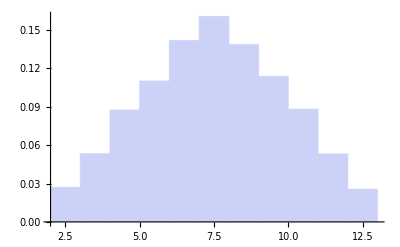

```mathematica
SetDirectory[NotebookDirectory[]];
<<Dice`
?Roll
Table[Roll,{i,1,20}]
Histogram[Table[Roll,{i,1,10^4}],Automatic,"Probability"]
```

## Programming applications (40 min)

### (#5) Matrix diagonalization (10 min)

In Lab 10 (linear algebra) you will learn how to diagonalize a matrix.  (If you haven’t had linear algebra yet, don’t worry too much about what this means.  You’ll learn more in lab 10.  To diagonalize a square matrix, you first use the Eigenvectors function to obtain the eigenvectors of the matrix.  Then you use the Transpose function to switch the rows and columns.    Next you take the transpose of the matrix of eigenvectors.   You then multiply the original matrix on the left by the inverse of this matrix and on the right by the original matrix of transposed eigenvectors.  The result is a matrix with the eigenvalues of the original matrix along the diagonal and 0’s everywhere else.  We will illustrate how this is done with the an example matrix a.  Here is an example of how you could do this set of steps on the matrix {{1/2,-1,2},{2,1,3},{1,1,1}}.

```mathematica
hisa={{1/2,-1,2},{2,1,3},{1,1,1}}
b=Eigenvectors[hisa]
c=Transpose[b]
d=Inverse[c].a.c
e=Simplify[d]
e//MatrixForm
```

(1/2 | -1 | 2
2 | 1 | 3
1 | 1 | 1)

(-8/5+3/20 (5+√41) | 3/5+1/10 (5+√41) | 1
-8/5+3/20 (5-√41) | 3/5+1/10 (5-√41) | 1
-2 | 1 | 1)

(-8/5+3/20 (5+√41) | -8/5+3/20 (5-√41) | -2
3/5+1/10 (5+√41) | 3/5+1/10 (5-√41) | 1
1 | 1 | 1)

(-(5 (27/20-(7 √41)/20))/(√41)-(15 (1/10-(√41)/10))/(√41)-(10 (-23/20+(3 √41)/20))/(√41)+(-(10 (27/20-(7 √41)/20))/(√41)-(10 (1/10-(√41)/10))/(√41)-(5 (-23/20+(3 √41)/20))/(√41)) (3/5+1/10 (5+√41))+(-(15 (27/20-(7 √41)/20))/(√41)-(5 (1/10-(√41)/10))/(√41)-(10 (-23/20+(3 √41)/20))/(√41)) (-8/5+3/20 (5+√41)) | -(5 (27/20-(7 √41)/20))/(√41)-(15 (1/10-(√41)/10))/(√41)-(10 (-23/20+(3 √41)/20))/(√41)+(-8/5+3/20 (5-√41)) (-(15 (27/20-(7 √41)/20))/(√41)-(5 (1/10-(√41)/10))/(√41)-(10 (-23/20+(3 √41)/20))/(√41))+(3/5+1/10 (5-√41)) (-(10 (27/20-(7 √41)/20))/(√41)-(10 (1/10-(√41)/10))/(√41)-(5 (-23/20+(3 √41)/20))/(√41)) | -(15 (27/20-(7 √41)/20))/(√41)-(25 (1/10-(√41)/10))/(√41)-(15 (-23/20+(3 √41)/20))/(√41)-2 (-(15 (27/20-(7 √41)/20))/(√41)-(5 (1/10-(√41)/10))/(√41)-(10 (-23/20+(3 √41)/20))/(√41))
-(5 (-27/20-(7 √41)/20))/(√41)-(15 (-1/10-(√41)/10))/(√41)-(10 (23/20+(3 √41)/20))/(√41)+(-(10 (-27/20-(7 √41)/20))/(√41)-(10 (-1/10-(√41)/10))/(√41)-(5 (23/20+(3 √41)/20))/(√41)) (3/5+1/10 (5+√41))+(-(15 (-27/20-(7 √41)/20))/(√41)-(5 (-1/10-(√41)/10))/(√41)-(10 (23/20+(3 √41)/20))/(√41)) (-8/5+3/20 (5+√41)) | -(5 (-27/20-(7 √41)/20))/(√41)-(15 (-1/10-(√41)/10))/(√41)-(10 (23/20+(3 √41)/20))/(√41)+(-8/5+3/20 (5-√41)) (-(15 (-27/20-(7 √41)/20))/(√41)-(5 (-1/10-(√41)/10))/(√41)-(10 (23/20+(3 √41)/20))/(√41))+(3/5+1/10 (5-√41)) (-(10 (-27/20-(7 √41)/20))/(√41)-(10 (-1/10-(√41)/10))/(√41)-(5 (23/20+(3 √41)/20))/(√41)) | -(15 (-27/20-(7 √41)/20))/(√41)-(25 (-1/10-(√41)/10))/(√41)-(15 (23/20+(3 √41)/20))/(√41)-2 (-(15 (-27/20-(7 √41)/20))/(√41)-(5 (-1/10-(√41)/10))/(√41)-(10 (23/20+(3 √41)/20))/(√41))
-5/2-11/2 (3/5+1/10 (5+√41))-11/2 (-8/5+3/20 (5+√41)) | -5/2-11/2 (3/5+1/10 (5-√41))-11/2 (-8/5+3/20 (5-√41)) | 3)

(43/(√41) | 181/40-1601/(40 √41) | -3+13/(√41)
181/40+1601/(40 √41) | -43/(√41) | -3-13/(√41)
1/8 (-31-11 √41) | 1/8 (-31+11 √41) | 3)

(43/(√41) | 181/40-1601/(40 √41) | 13/(√41)-3
181/40+1601/(40 √41) | -43/(√41) | -3-13/(√41)
1/8 (-31-11 √41) | 1/8 (11 √41-31) | 3)

You already know that a function can input and output general expressions, not just numbers.  Use Module to define a function diagonalize[matrix_], which takes a square numerical matrix as input and returns its diagonal form as output.  After you Simplify the diagonalized matrix, the module should return its MatrixForm.  Test your function on the matrix {{1, 2, 3}, {2, 1, 2}, {3, 2, 1}}.

```mathematica
a ={{1,2,3},{2,1,2},{3,2,1}};
diagonalize[Matrix_]:=Module[{b,c,d,e},
b = Eigenvectors[Matrix];
c = Transpose[b];
d = Inverse[c].a.c;
e = Simplify[d];
e//MatrixForm
]
```

```mathematica
diagonalize[a]
```

(1/2 (5+√41) | 0 | 0
0 | -2 | 0
0 | 0 | 1/2 (5-√41))

### (#6) Polynomial roots (10 min)

(a) Plot x^3-3x + r over the range {x, -3, 3} with PlotRange→{-10,10} as an option, and Manipulate the plot as r varies over the range {r, -5, 5}.  Observe that the number of roots (i.e. points where y(x) = 0) depends on r.

```mathematica
Manipulate[Plot[x^3-3x+r,{x,-3,3},PlotRange->{-10,10}],{r,-5,5}]
```

(b) Use Module to create an argumentative function f[r_] that takes a real number r as input, solves the equation x^3-3x +r==0 (using Solve) and returns the solution as a list of three decimal numbers.  Evaluate this function at each integer r  value from -3 to 3.  If you see small imaginary round-off errors in results that would otherwise be real, add a step within the module to Chop anything less than 10^-10 down to zero.  Note that we expect you to use a couple of local variables inside the module.

```mathematica
func[r_]:=Module[{list, chopped},
list =Solve[x^3-3x+r==0,x];
chopped = Chop[list]
]
func[-5]
```

{{x→1/3 (135/2-(27 √21)/2)^(1/3)+(1/2 (5+√21))^(1/3)},{x→-1/6 (1+ⅈ √3) (135/2-(27 √21)/2)^(1/3)-1/2 (1-ⅈ √3) (1/2 (5+√21))^(1/3)},{x→-1/6 (1-ⅈ √3) (135/2-(27 √21)/2)^(1/3)-1/2 (1+ⅈ √3) (1/2 (5+√21))^(1/3)}}

### (#7) Root finder (20 min)

(a) Evaluate the cell below to define and plot a function that has irregularly spaced roots.

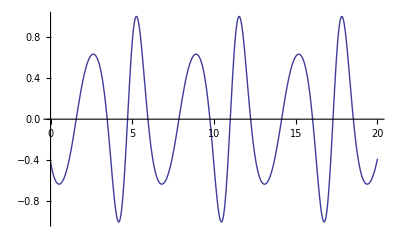

```mathematica
funky[x_] :=Cos[x+2*Cos[x]]
Plot[funky[x],{x,0,20}]
```

(b) In the cell below, create a Module, rootfinder[func_, {min_, max_, step_}], that numerically finds all the roots of a smooth function, f(x), within a specified range.  The first argument, func, can either be a function name (e.g. Cos) or a pure function (Cos[#]&), but not an expression (e.g. Cos[x]).  The second argument should be a list of three numbers.  Then use your rootfinder to find all of the roots of f(x)=cos(x+2cos(x)) between x = 0 and 20.  No root should appear more than once in the output.

Hints:  As Table iterator n goes from from min to max in increments of step (you will need to choose step wisely) use FindRoot to locate a root near each value of n.  After you have done this, Round the results to the nearest millionth, use Union to eliminate duplicates, convert (N) results back into decimal form, and Select the ones that lie between min and max.

```mathematica
rootFinder[func_,{min_,max_,step_}]:=Module[{values,roots,unique,rounded},
values=Table[n,{n,min,max,step}];
roots=x/.(FindRoot[func[x],{x,#}]&/@values);
rounded = Round[roots,.000001];
unique= Union[rounded]//N;
Select[unique,min<#<max&]
]
```

```mathematica
rootFinder[funky,{0,20,1}]
```

{1.5708,3.46629,4.71239,5.95849,7.85398,9.74948,10.9956,12.2417,14.1372,16.0327,17.2788,18.5249}

### Quadratic approximations (optional)

Given a smooth function f(x), we can take three evenly-spaced sample points on the curve and then approximate y(x) with the parabola, g(x)=a x^2+b x+c, that runs through the points.  When the sample points are reasonably close together, g(x) provides a very simple means of computing approximate derivatives and integrals.

(a) Evaluate the cells below, where we start with an arbitrary function, y(x), and create three equations by setting y(x)=a x^2+b x+c at each sample point, x_0-h,  x_0  and  x_0+h.  These three equations are then solved to obtain the unknown coefficients {a, b, c} in terms of the center point (x_0), the spacing (h) and the sample values of y(x).  Explain the meaning of the output to your TA.

```mathematica
Clear[a,b,c]
g[x_] := a*x^2+b*x+c
equations = {y[x0-h]==g[x0-h],y[x0]==g[x0],y[x0+h]==g[x0+h]}
abcrule =Solve[equations,{a,b,c}][[1]]
```

(b) In the cell below, we define seepoly[func_, center_, spacing_, hpr_], a module that must Plot a function, y(x), and its quadratic approximation, g(x), on the same graph.  Evaluate the cell, explore the resulting animation, study the code within the module, and explain to your TA how what each step does.

```mathematica
seepoly[func_,center_,spacing_,hpr_] :=Module[{myrule,mypoly,plots,spots},
myrule =  {y->func,x0->center,h->spacing};
mypoly = g[x]/.abcrule/.myrule;
plots = Plot[{func[x],mypoly},{x,center-hpr,center+hpr},PlotRange->All,PlotStyle->{{Thick,Red},{Thick,Blue}}];
spots =Point[{#,func[#]}]&/@{center-spacing,center,center+spacing};
Show[{plots, Graphics[{PointSize[0.02],spots}]}]
]

Manipulate[seepoly[Cos,c,s,Pi],{c,0,Pi},{s,0.01,Pi}]
```

(c) In the cell below, use g[x]/.abcrule to obtain approximate values for y'(x_0),  y''(x_0) and  ∫_(x_0-h)^(x_0+h) y(x)ⅆx.  Hints: Use the "primed" notation (shorthand for Derivative) for your derivatives, and Simplify each result.  The integral approximation that you will obtain is known as Simpson's rule.

(d) In this cell, we have started to define calcpoly[func_, center_, step_], a module that takes three inputs: (1) a function name or a pure function of one variable, (2) a numerical value for x_0, and (3) a numerical value for h.  Your job is to complete this module to compute quadratic approximations to the following four quantities: y(x_0),  y'(x_0),  y''(x_0) and  ∫_(x_0-h)^(x_0+h) y(x)ⅆx.  Your module won't return any output; but it will Print both the actual and approximate values of each of these quantities.

Try calcpoly on both ⅇ^(-x^2) and cos(x) when x_0=0.0 and h = 0.5.  

Hints: First, define a local replacement rule, myrule = {y → func, x0 → center, h → spacing}.  Compute each of the derivatives and integrals  y(x_0),  y'(x_0),  y''(x_0), ∫_(x_0-h)^(x_0+h) y(x)ⅆx,  g(x_0),  g'(x_0),  g''(x_0) and  ∫_(x_0-h)^(x_0+h) g(x)ⅆx) symbolically, and apply abcrule and/or myrule to each quantity, assigning a local name to each result.  Take care not to assign definitions to global variables {g, y, x0, h}, which we are already using.  Be sure to feed calcpoly a function name (e.g. Cos) or a pure function (Cos[#]&), but not an expression (e.g. Cos[x]).

```mathematica
calcpoly[func_,center_,spacing_] := Module[{myrule,yexact,yapprox,d1exact,d1approx,d2exact,d2approx,intexact,intapprox},


Print["y(x0) = ",yexact," ≈ ",yapprox];
Print["y'(x0) = ",d1exact," ≈ ",d1approx];
Print["y''(x0) = ",d2exact," ≈ ",d2approx];
Print["∫_(x0 - h)^(x0 + h) y(x)ⅆx = ",intexact," ≈ ",intapprox];
]

calcpoly[Cos[#]&,0.0,0.5]
```

## Procedural flow control (10 min)

There are times when you will want to interrupt the sequence of evaluations being performed within a program.  You might wish to terminate (Break) out of a loop when its objective has been reached early, or skip (Continue) past a few unnecessary steps, or Pause to review some intermediate output, or Interrupt a job to briefly work on something else, or Abort an excessively-long or problematic computation before completion.  Refer to the DC reference pages of the appropriate Flow Control functions as needed.

Note that some flow control operations (e.g. Throw and Catch) not only terminate a loop, but can also return the values of user-specified loop variables.  We will defer the discussion of this kind of operation in the next section.

### (#8) How to change lanes (5 min)

Evaluate the cells below in sequence, and compare and constract the behaviors of Break, Continue, Abort and Interrupt for your TA.

When you evaluate the Interrupt example, try each of the buttons provided in the popup-dialog window.   After pressing the "Enter Subsession" button, check the value of the n iterator in a new cell and then type Return[] to exit the subsession.  While inside the subsession, the "Running..." indicator in the status bar at the top of this window reminds you that the original calculation is still waiting.

```mathematica
Do[If[n==5,Break[]];Print[n],{n,1,10}];
```

1

2

3

4

```mathematica
Do[If[n==5,Continue[]];Print[n],{n,1,10}];
```

1

2

3

4

6

7

8

9

10

```mathematica
Do[If[n==5,Pause[2]];Print[n],{n,1,10}];
```

1

2

3

4

5

6

7

8

9

10

```mathematica
Do[If[n==5,Abort[]];Print[n],{n,1,10}];
```

1

2

3

4

$Aborted

```mathematica
Do[If[n==5,Interrupt[]];Print[n],{n,1,10}];
```

1

2

3

4

5

6

7

8

9

10

### (#9) User input (5 min)

There are many ways to make a program stop and ask for user input.  Evaluate the cells below to see several possibilities, which are listed in order of increasing complexity.

```mathematica
res = InputString[];
"My name is "<> res <> "!"
```

My name is hi!

Cos[x]

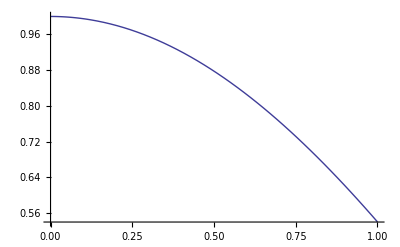

```mathematica
res =Input["Enter an expression containing x."]
Plot[res,{x,0,1}]
```

```mathematica
G
```

```mathematica
res = 0;
Do[res += ChoiceDialog["Make 3 selections, which will then be added together.",{" 1 "->1," 2 "->2," 3 "->3," 4 "->4," 5 "->5}],{3}]
res
```

10

```mathematica
waitforuser := DialogInput[DialogNotebook[{Button["Click 3 times to return to Kansas",DialogReturn[]]}]]
Do[waitforuser,{3}];
```

```mathematica
pickcolor=DialogInput[{col=Pink},
DialogNotebook[{TextCell["Click colored box below to pick a color"],ColorSetter[Dynamic[col]],Button["Proceed",DialogReturn[col]]}]
]

Graphics[{pickcolor,Disk[]},ImageSize->100]
```

RGBColor[0.,0.,1.]

-Graphics-

If you really want to get fancy with your user interface beyond these simple input forms, you can build a whole Grahical User Interface (GUI).  One approach is to use the GUIKit package in Mathematica.  It is somewhat cumbersome compared to options I prefer using J/Link or NETLink to link to a GUI written in Java or in a .NET language such as C# or Visual Basic.  A GUI of that sophistication is beyond the scope of this course.

```mathematica
Testing
```

Testing

### (#10) Conditional Definitions (5 min)

For some functions, it may only make sense to define them for certain conditions.

The /; operator when applied to a definition, means that the definition only applies then the test following the rule yields true.  Here is an example.  (The first line removes all definitions of f which might already exist.)

```mathematica
If[NameQ["f"],Remove["f"]]
f[x_]:=Sqrt[x]/;x≥0
f[2]
f[-5]
```

√2

f[-5]

The function f[2] returns unevaluated because the function definition only applies when x>3.  If there are several overlapping possible definitions, the definitions are used in the order they were made until one matching the condition can be found.  Here is an example of an alternate way to implement the UnitBox function.

```mathematica
If[NameQ["fs"],Remove["fs"]]
fs[x_]:=1/;Abs[x]≤1
fs[x_]:=0
fs[0.5]
fs[1.5]
```

1

0

You can find out which definitions exist for a symbol using ??.

```mathematica
??fs
```

Global`fs

fs[x_]:=1/;Abs[x]≤1
 
fs[x_]:=0

## Testing (25 min)

One of the challenges of computaional physics is making sure you believe your results.  Sometimes its pretty obvious when a program is giving a wrong answer (when Mathematica gives you an error message, for instance).  In other cases, it requires some care to make sure your computations are producing the results you expect.  In this section we will discuss strategies for testing your code and verifying that it is working as expected.

### Use Modular Code

An important concept in effective testing of code is “divide and conquer.”  This consists of breaking your code into isolated units with well-defined interfaces.  This let’s you test each piece independently and isolate where any problems are.  Breaking a large monolithic computation into functions, modules, and packages will pay off in the long run.  It will be easier to isolate problems, the code will be easier to understand, it will be simpler to make changes in the code, and it will be easier to reuse parts of the current project in other projects.

For example, consider the following program to find the allowed radial electron energy levels below 3 eV in nanowires of radius 1.5 nm.  (Don’t worry about the physics for now.  Jsut look at the organization.)

```mathematica
c=3*10^17;
(* nm/s *)
me=0.511*^6; (* eV/c^2*)
hbar =6.58212*^-16;  (* eV-s *)
(* Radial equation *)
radEqn = r^2 R''[r]+r R'[r]-m^2 R[r]==-2 me/(hbar*c)^2 e r^2 R[r];
soln = DSolve[radEqn ,{R[r]},r];
(* pick out the two independent solutions *)
rsol = R[r]/.soln//First; (* pick out solution from the list *)
r1 =rsol/.{C[1]->1, C[2]->0} ;
r2 = rsol/.{C[1]->0,C[2]->1};
(* Find roots with zero on the boundary of a circle of radius a*)
a=1.5;
rf=r1/.{r->a,m->0}//Chop;
rone[e_]:=Evaluate[rf]
rg = r2/.{r->a,m->0}//Chop;
rtwo[e_]:=Evaluate[rg]
(* Convert these into functions so I can find roots for r=0 and m=0 *)
Table[FindRoot[rone[e],{e,i}],{i,0.1,3,0.1}];
e/.%;
l1=Select[Union[Map[Round[#,0.00001]&,%]],#<3&];
Table[FindRoot[rtwo[e],{e,i}],{i,0.1,3,0.1}];
e/.%;
l2=Select[Union[Map[Round[#,0.00001]&,%]],#<3&];
Union[Join[l1,l2]]
(* then a lot more stuff repeating this for other m values *)
(* At this point I gave up finding the roots for other m values and debugging this further *)
```

{0.09806,0.2656,0.51669,0.85143,1.26983,1.77191,2.35766}

We ran into all kinds of problems getting this to work when written this way.  Variables interfered with each other, things got redefined in unexpected places, it duplicated functionality was done correctly in one place and incorrectly in others.   As a matter of fact, there are some problems with illegal roots, disallowed zero energies, zero wave functions and others which were never fixed in this version it had become so complicated.  Consider the following version which was much easier to get running and alter.

```mathematica
Clear["Global`*"]
(* Setup constant *)
a=1; (* radius of wire in nm *)
(* Create equation: c, me, and hbar are now local *)
radEqn = Module[{c=3*^17,(* speed of light in nm/s *)
me=0.511*^6,(* electron mass in eV/c^2 *)
hbar=6.58212*^-16}, (* hhbar in eV-s *)
r^2 R''[r]+r R'[r]-m^2 R[r]==-2 me/(hbar*c)^2 e r^2 R[r]
];
soln = R[r]/.DSolve[radEqn, R[r],r]//First;
makeFunc[n_]:=Module[{subf},
subf=soln/.{C[1]->n, C[2]->(1-n)};
subf/.{r->a}//Chop
];
(* Select the function which is finite at the origina *)
oval0 = makeFunc[0]/.{m->0,e->0};
r[e_]:= Evaluate[If[Abs[oval0]<Infinity,makeFunc[0], makeFunc[1]]]
(* Only one of these will be regular at 0, find it *)
uniqueRoots[f_,order_]:=Module[{allRoots},
 Off[FindRoot::lstol];
allRoots = Table[FindRoot[f[e]/.m->order, {e,i}],{i,0.1,3,0.1}];
On[FindRoot::lstol];
allRoots = e/.allRoots;
Select[Union[Map[Round[#, 0.000001]&, allRoots]], 0<#<3&]
]
append[f_]:=Module[{nlst, lst={}, order=0},
While[Length[(nlst=uniqueRoots[f, order])]>0 && order < 10,
lst=Join[nlst, lst];
order++
];
Union[lst]
]
append[r]
```

{0.220643,0.560154,1.00626,1.16256,1.55305,1.87781,2.19693,2.70311,2.85713,2.93541}

### Plan Ahead

It is a good idea to think about what you expect your code to compute before you begin actually writing it.  What would a right answer look like?  How will the modules and packages interact with each other?  Are there sections of the computations which might consume a lot of resources (CPU time, memory, disk space, network access, etc.)?  If so, how might these be optimized.  Are there functions or libraries already available which might save you some time?

Code that is not well-planned in advance often ends of full of complicated logic and convoluted flow of execution to handle special cases which a tacked on as the project evolves.  This makes the code complex and difficult to maintain.

### Test the Extremes

The cases where problems are most often occur are at the limits of your calculations.  Make sure the extreme values are part of your tests.

As an example, consider the following program we wrote to test and see if three points in 3D are colinear.  My algorithm notes that if thay are colinear, the ratio of the change in distance in each dimension will be the same.  The module colinear computes these ratios and then checks to see if they are equal.  It is very efficient compared to an alternative approach I used earlier.

```mathematica
colinear[p1_, p2_, p3_]:=Module[{alpha},
alpha=(p3-p1)/(p2-p1);
alpha[[1]]==alpha[[2]] ==alpha[[3]]
]
```

We first tested it with three points we knew were colinear to make sure it returned true.  It passed that test great.

```mathematica
colinear[{1,1,1},{2,2,2},{3,3,3}]
```

True

Next we tested to make sure it worked with three points we was sure were not along the same line.

```mathematica
colinear[{1,2,3},{-1,4,7},{0,9,-6}]
```

False

We were starting to feel like this might be a great solution for our problem.  However, there was a problem.  (Have you spotted it already?)  We tried an extreme case of the three points lying along a coordinate axis (the x axis in this case).

```mathematica
colinear[{1,0,0},{2,0,0},{3,0,0}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

2==Indeterminate==Indeterminate

The routine failed the test because we forgot to consider the possibility that the denominator in the computation of alpha could be zero.

### Build a Test Suite

Build a set of expected inputs and their associated outputs that you are pretty sure are correct.  Each time you make a change in the code rerun these test cases to make sure they still work.  If you ever find the code generating a wrong answer in a particular situation, add a test case that will be guarenteed to fail if that particular problem ever creeps into the code again.

We had an interesting conversation with an engineer responsible for maintaining a complicated control program for missle defense at Hill Air Force Base.  He studied the process of maintining code and tracked how the number problems in the code changed as code was refined.  He discovered that mature code often gets to the point where changes meant to fix the code introduce as many errors as they fix.  A good test suite can spot these situations and great improve code reliability.

```mathematica
fc[x_]:=1+x^2 (-1/2+x^2 (0.041666666666666664+x^2 (-0.001388888888888889+x^2 (0.0000248015873015873-2.755731922398589*^-7 x^2))))
f[0.1]-Cos[0.1]
```

-0.995004+f[0.1]

Let’s develop an automatic test suite for this function.  I’d like to make it so that its easy to add cases, and gives me some information about how well it has done.  Let’s start by making a list of correct answers.

```mathematica
correct = Table[{x,Cos[x]},{x,-0.1,0.1,0.001}];
```

Now we’ll make a test unit which will check the function.

```mathematica
testFc[correct_]:=Module[{result, tolerance=10^-7},
result = Map[Abs[fc[#[[1]]]-Cos[#[[1]]]]<tolerance&,correct];
(* Print the results *)
Print[StringForm["ran `` tests on fc",Length[correct]]];
Print[StringForm["  `` passed", Count[result, True]]];
Print[StringForm["  `` failed", Count[result, False]]];
]
```

```mathematica
testFc[correct]
```

ran 201 tests on fc

201 passed

0 failed

If at some point you notice that the test is missing an important case, you can add it in.

```mathematica
correct=Append[correct,{10,Cos[10]}];
```

You if you rerun the test, you’ll find it has an additional test which fails.

```mathematica
testFc[correct]
```

ran 202 tests on fc

201 passed

1 failed

You could get a little fancier and make sure you know about any failed tests if the tests were buried in a notebook where you were evaluating the entire thing.

```mathematica
visualTestFc[correct_]:=Module[{result, tolerance=10^-7, failures},
result = Map[Abs[fc[#[[1]]]-Cos[#[[1]]]]<tolerance&,correct];
(* Print the results *)
Print[StringForm["ran `` tests on fc",Length[correct]]];
Print[StringForm["  `` passed", Count[result, True]]];
failures = Count[result, False];
Print[StringForm["  `` failed", failures]];
(* Big alert *)
If[failures>0,MessageDialog[StringForm["The test suite failed `` tests", failures]]];
]
```

```mathematica
visualTestFc[correct]
```

ran 202 tests on fc

201 passed

1 failed

### Find Analytical Test Cases (5 min)

In many cases, you may be able to find simple cases which have known solutions.  Perhaps another well-tested program has run a problem similar to yours you can compare your answer against.

An example of this case is a program we once worked on to compute the effects of scattering electromagnetic waves from aribtrarily shaped objects.  There were no exact answers for the problems we were most interested in.  However, we could use the code to compute what would happen when we scattered from simple shapes like spheres, plates, and cylinders which could be computed analytically or with simple series.  Once our program computed results which agreed with these canonical cases, we had more confidence in the answers we found for more complicated objects.

Here is an example of a program we wrong to compute the amplitude of a pendulum as a function of time without using the small angle approximation.  The pendulum is assumed to have an amplitude amp_ and speed 0 at time t=0.

```mathematica
g=9.8;
l=3;
highPendulum[l_, amp_]:=Block[{eqn, soln, th, theta, expr},
eqn=theta''[t]==-g/l Sin[theta[t]];
Off[Solve::ifun];
soln=DSolve[eqn,theta[t],t];
On[Solve::ifun];
expr=theta[t]/.soln[[2]];
expr = expr/.{C[1]->c1, C[2]->c2};
th[t_]:=Evaluate[expr];
initCond = FindRoot[{th[0]-amp,th'[0]},{c1,-1.5},{c2,0.5}];
th[t]/.initCond//Chop
]
```

It is instructive to compare the results of this calculation to that using the small angle approximation.

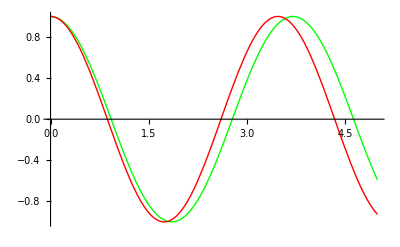

```mathematica
amp=1.0;
th1[t_]:=Evaluate[highPendulum[l, amp]];
Plot[{th1[t],amp*Cos[Sqrt[g/l]t]},{t,0,5},PlotStyle->{Green,  Red}]
```

The period of the pendulum in the exact case is a little longer than with the small angle approximation.  This makes sense if you think about it a bit.  Since sin(θ) is gets smaller than θ as θ increases, the torque at the top of the swing will be less than that computed in the small angle approximation.  Since the torque is smaller, it takes longer for the pendulum to complete the period of its swing.  This “reasonableness” kind of thinking is a good check on numerical answers.  If I had seen a smaller period, I would worry that I had a sign wrong somewhere or another numerical problem.

A good test case for this code is to see if we get the same answer as the small angle approximation when the amplitude is small.  Try an amplitude of 0.1, which shoudl be a region that the small angle approximation works.  Discuss your result with your TA.

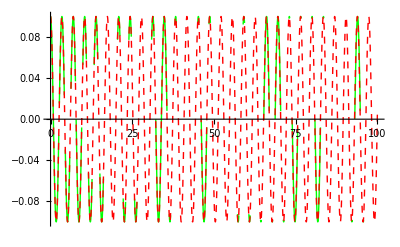

```mathematica
amp=0.1;
th1[t_]:=Evaluate[highPendulum[l, amp]];
Plot[{th1[t],amp*Cos[Sqrt[g/l]t]},{t,0,100},PlotStyle->{Green,  {Red,Dashed}}]
```

### Program Defensively

At different places in your program, think about what kinds of answers and parameters you expect to be passed to your routines.  Check and make sure functions are called with the kinds of arguments you expect.  If you expect a result to be positive or real, check and see if that is the case.

Sometimes writing these checks into the code can add unacceptable overhead to computation time.  In this case, you can have testing and production versions of the module with identical interfaces.  In the testing phase, you run with the slower version that looks for problems.  In the production phase you can use the streamlined version.

As an example, consider the following inefficient program that computes x to a power.  The algorithm will succeed if supplied with an integer power, but will fail otherwise.

```mathematica
pow[x_,n_]:=Module[{prod=1},
Do[prod *= x,{i,1,n}];
prod
]
pow[x,3]
pow[x,3.5]
pow[x,-2]
```

x^3

x^3

1

It gives the correct answser for positive integers, but gives an incorrect answser for negative integers or real numbers.  Writing it as follows warns the caller about the problem.

```mathematica
pow2[x_,n_Integer]:=Module[{prod=1},
If[n≥0,
Do[prod *= x,{i,1,n}],
prod="n must be non-negative"];
prod
]
pow2[x,3]
pow2[x,3.5]
pow2[x,-2]
```

x^3

pow2[x,3.5]

n must be non-negative

There are some better ways to deal with problem arguments using Message, Assert, or Abort.

### (#10) Message (5 min)

The Message function prints a formatted message associated with your function that can be turned On and Off.  Explain the following output to your TA.

```mathematica
If[NameQ["pow3"],Remove["pow3"]]
pow3::nint = "pow3 called with `1` which is not an integer";
pow3::neg = "pow3 called with `1` which is not positive";
pow3[x_,n_]:=Module[{prod=Null},
If[n<0,Message[pow3::neg,n],
If[IntegerQ[n],
prod=1; Do[prod *= x,{i,1,n}],
Message[pow3::nint, n]]
];
prod
]
{pow3[x,3], pow3[x,3.5], pow3[x,-2]}
Off[pow3::nint];
{pow3[x,3], pow3[x,3.5], pow3[x,-2]}
```

pow3::nint: pow3 called with 3.5 which is not an integer

pow3::neg: pow3 called with -2 which is not positive

{x^3,Null,Null}

pow3::neg: pow3 called with -2 which is not positive

{x^3,Null,Null}

### (#11) Assert (5 min)

The Assert function is a quick way to combine a condition test with a message.  Unfortunately, this means you lose control of other things you might want to do to shape the returned result.  Explain the following output to your TA.

```mathematica
If[NameQ["pow3"],Remove["pow3"]]
pow3[x_,n_]:=Module[{prod=1},
Assert[n≥0];
Assert[IntegerQ[n]];
Do[prod *= x,{i,1,n}];
prod
]

On[Assert]
{pow3[x,3], pow3[x,3.5], pow3[x,-2]}
Off[Assert];
{pow3[x,3], pow3[x,3.5], pow3[x,-2]}
```

Assert::asrtf: Assertion IntegerQ[3.5] failed.

Assert::asrtf: Assertion -2 ≥ 0 failed.

{x^3,x^3,1}

{x^3,x^3,1}

### (#12) Abort (5 min)

Sometimes you will encounter conditions that make it impossible or dangerous to continue a calculation.  This is when Abort comes in handy.  Write a function which will sum the numbers from 1 to n, but will abort if the caller supplies an argument larger then 10^7.  Provide two test cases, one which fails and the other which doesn’t

```mathematica
mySum[n_]:=Module[{result},
result = If[n>10^7,Abort[],Sum[i,{i,1,n}]]
]
mySum[3]
mySum[10^7]
mySum[10^7+1]
```

6

50000005000000

$Aborted

## Debugging (20 min)

Debugging could be described as the process of figuring out why your code is not working properly.  This process requires that you know what your code should be doing, and also the ability to find out what it actually is doing.  In this section, we will present some simple debugging concepts and tools for monitoring the status of a calculation.  These tools will be useful to you when you need to debug your own programs.

With modules and packages of any significant complexity, you will probably spend more time debugging your program than writing it the first time.  Be systematic and don’t be discouraged.  Mathematica gives you a rich set of tools to isolate and fix problems.  Debugging is a natural outgrowth of well-designed tests.

### (#11-#13) Critical Functions (20 min)

#### (#11) Print (5 min)

The Print function is the easiest way to monitor the value of a variable within a loop.  We have used this function several times during the past few labs.  Print doesn't return output that can be passed to another function.  It simply displays its argument in the notebook window for the user.

```mathematica
Sum[Print[i];i,{i,1,10}]
```

1

2

3

4

5

6

7

8

9

10

55

Add one or more Print statements to the following module to diagnose why it returns a complex answer for the case of x=1.5.

```mathematica
func[x_]:=Module[{y, z},
y=1.9 x;
While[y>0.5,
z=Cos[y]^2;
y=Sqrt[Log[z]];
]
Print[Log[z]]
z
]
func[1.5]
```

Greater::nord: Invalid comparison with 0.  + 0.293699\ ⅈ
 attempted.

-0.0862592

0.917356 Null^2

#### (#12) Throw and Catch (10 min)

Throw and Catch not only work to terminate a loop, but also return information at the time of termination.  The information tagged by Throw is returned as output by the nearest Catch.  In practice, Throw is usually used to flag an error condition or unexpected argument.  Catch can then be used to decide whether to continue the calculation, substitute another value, print an error message, or abort the calculation.

```mathematica
temp = 1; counter = 0; 
Catch[While[Abs[temp] > 0.0005, temp = RandomReal[]; If[++counter >= 1000, 
     Throw[{"Limit exceeded!", counter}]]]]
counter
```

{Limit exceeded!,1000}

1000

Write a function exp[x_] that returns ⅇ^x if x<10 but throws an error with tag overflow and returns ⅇ^10 if x≥10.  Demonstrate how this funcition works without a Catch for exp[5] and exp[20].  Then demonstrate what happens if Catch is used with the tag overflow for exp[20].

```mathematica
exp[x_]:=If[x<10,Exp[x],Throw[Exp[10],overflow]]
exp[5]
exp[20]
Catch[exp[30],overflow]
```

ⅇ^5

Throw::nocatch: Uncaught Throw[ⅇ^10, overflow] returned to top level.

Hold[Throw[ⅇ^10,overflow]]

ⅇ^10

#### (#13) Catching Messages and Aborts (5 min)

You can also intercept a Message or an Abort similarly to how you Catch a Throw.  The Check function checks to see if any messages were generated by your call.  It returns an alternate answer in the case of a message.  Explain the output of the following cell to your TA.  The function slope computes the slope of a line passing through two points.

```mathematica
slope[p1_, p2_]:=(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])
slope[{1,3},{2,7}]
slope[{1,3},{1,7}]
Quiet[Check[slope[{1,3},{1,7}],∞]]
```

4

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

∞

### Optional Functions

#### Evaluation Monitor

A good tutorial on Monitoring Algorithms compares EvaluationMonitor and StepMonitor, two options that are allowed inside many routines that either plot or numerically operate on mathematical functions (e.g. Plot, NIntegrate, Minimize, etc).  The EvaluationMonitor option does something each time the function being worked on gets evaluated.  In the example below, it increments our local evals variable.  The StepMonitor option does something each time the parent algorithm (e.g. Minimize) makes a successful step, which might involve several function evaluations.  In the example below, it increments our local steps variable.

The algmonitor module that we have defined here not only finds the two-dimensional minimum point of a complicated function, but returns the number of function evaluations and the number of search steps required to find it using a user-specified search algorithm.

```mathematica
algmonitor[method_] :=Module[{evals= 0,steps=0},
FindMinimum[(x-1)^2+100(y-x^2)^2,{{x,-1},{y,1}},Method->method,EvaluationMonitor:>evals++,StepMonitor:>steps++];
{method,evals,steps}
]

algmonitor/@ {Automatic,"LevenbergMarquardt","InteriorPoint","Newton","QuasiNewton", "ConjugateGradient","Gradient"}

TableForm[%,TableHeadings->{{},{"Method","Evaluations","Steps"}} ]
```

#### Sow and Reap

(a) Sow and Reap work together much like Throw and Catch.  Sow, however, does not terminate any loops, but rather accumulates a list of tagged information that is eventually returned as output by the nearest Reap.  Evaluate the following two cells, which perform identical operations, except for the variable-sampling performed along the way by Sow and Reap.

```mathematica
res  = 0;
Do[res = res+i,{i,1,10}]
res
```

```mathematica
res  = 0;
Reap[Do[res = res+i; Sow[res],{i,1,10}]]
res
```

(b) This is a somewhat more interesting example that shows the points sampled during a one-dimensional numerical integration of f(x)=√x.  The Sow operation was used within the EvaluationMonitor option of NIntegrate.  NIntegrate includes this option just in case someone wants to take a look under the hood.

```mathematica
f[x_] :=Sqrt[x]
{result,{points}} = Reap[NIntegrate[f[x],{x,0,1},PrecisionGoal->4,EvaluationMonitor:>Sow[{x,f[x]}]]]
Show[Plot[f[x],{x,0,1}],Graphics[Point/@points]]
```

#### Monitor

Mathematica's Monitor function allows the user to monitor the progress of a lengthy computation.  Evaluate the following two examples.  In the first example, which repeatedly evaluates the average of 10^6 random numbers, we implement both numeric and graphical monitors.  In the second example, which we modified from the "Applications" section of the DC reference page, we fit a one-dimensional function to a set of data, while monitoring a plot of the fitting function.  Observe that monitors are temporary, disappearing after a computation has finished.

```mathematica
ranavg[num_]:=Sum[RandomReal[],{num}]/num;
Monitor[   Table[ranavg[10^6],{n,1,10}],  {n,ProgressIndicator[n,{0,10}]}   ]
```

```mathematica
data = {{0.18,-0.13},{0.84,-0.06},{0.05,0.88},{0.24,-0.63},{0.67,0.93},{0.05,0.88},{0.65,0.92},{0.01,0.99},{0.17,-0.04},{0.23,-0.55}};
lp = ListPlot[data, PlotRange->{-1,1},PlotStyle->{PointSize[0.02]}];

model[{a_, k_, w_, p_}] := a Exp[-k x] Sin[w x +p];
varlist = {a,k,w,p};

Monitor[FindFit[data, model[varlist],varlist,x,StepMonitor:>Pause[0.5]],Show[lp,Plot[model[varlist],{x,0,1}]]]
```

#### Trace

The Trace function lets us look under the hood by capturing the inputs received and the outputs returned at every step of a calculation.  Though the output can be pretty opaque, Trace is a powerful tool if you really need to know how your calculation is proceeding internally.

```mathematica
a = 2; b = 3;
crazy = Trace[Exp[2*(a+b+7)]]
crazy//TreeForm
crazy//InputForm
```

#### Mathematica Workbench

Debugging and maintaining large projects and packages is best done using the Mathematica Workbench.  This includes facilities for important debugging and testing procedures we haven’t had time and space to review here.  These include:

version control

unit testing

full featured debugger

break points

watch points

call stack

stepping

monitoring

## On Your Own (30 min)

Write a package which will translate voltage measurements from a temperature sensing diode into temperature.  The package should have a routine to call with calibration data (measured voltage/temperature pairs), a routine to call which takes a voltage and returns a temperature, and a routine to call for testing.  Be sure your tests check for appropriately handling the following conditions:

providing inputs within calibration limits

where voltages exactly match calibration voltages

where voltages are between calibration voltages

providing inputs outside calibration limits

providing inputs which have a wrong data type (string, for instance)

providing calibration data where the voltages and not stricly increasing or decreasing

You might find the Interpolation function helpful in this exercise.  Be sure your package is appropriately documented both for your own reference and so others will know how to use it.  Any data which is stored between calls should be private and not global.

Here is the calibration data.  The first number in of each pair is a voltage and the second number the temperature in Kelvin.

```mathematica
theData={{107.97661143675317,1.9900090719454193},{148.6923000122924,1.7707436134679264},{176.90564492163165,1.6229034973271557},{16.986009272807575,2.46351469610207},{190.75588793412516,1.544097704545851},{137.21427597874347,1.832416246014891},{116.79096336113136,1.958138047605583},{37.47560343337524,2.358506792969041},{148.18089978704614,1.7693512922939507},{30.508283755738418,2.405814449469174},{157.96394182463771,1.6992645810170925},{116.43206946261877,1.949081213417996},{178.34183449930978,1.6195753575106822},{132.72852946818014,1.8529397030092025},{178.94781961135678,1.612147000768918},{76.37488131962016,2.167933095119373},{64.33294897830152,2.223872800337109},{183.59678070648843,1.5944520983951989},{151.40943403271868,1.7620324465090833},{167.15847588777987,1.6784745802966434}};
```

InterpolatingFunction[{{1.5441,2.46351}},<>]

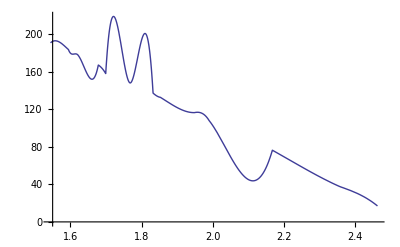

```mathematica
Calibrate[theData]
Plot[VoltToTemp[x],{x,1.5441,2.46351}]
```

```mathematica
hi = Interpolation[theData]
hi[107.9766]
Plot[hi[x],{x,1,5}]
```

InterpolatingFunction[{{16.986,190.756}},<>]

1.99001

```mathematica
check = Calibrate[data]
```

InterpolatingFunction[{{16.986,190.756}},<>]

### Optional

The data is a bit noisy.  Can you find a way to smooth out the noise in the data?  If you can, add that functionality to your package.

```mathematica
Clear["`*"]
```